```mathematica
nbdir=ToString[NotebookDirectory[]]<>"no-grid-factor/"
```

/home/mls/Code/multimode/no-grid-factor/

```mathematica
dir1=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid_K-kerns-fixed";
SetDirectory[dir1]
filename=FileNames["*h5"][[1]];
t2 = Import[filename, {"Datasets", "/1/t"}];
x2 = Import[filename, {"Datasets", "/1/x"}];
y2 = Import[filename, {"Datasets", "/1/y"}];
imatom2 = Import[filename, {"Datasets", "/1/imatom"}];
reatom2 = Import[filename, {"Datasets", "/1/reatom"}];
imlight2 = Import[filename, {"Datasets", "/1/imlight"}];
relight2 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq2 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq2= Import[filename, {"Datasets", "/1/modlight"}];
relightint2 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint2 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

Part::partw: Part 1 of {} does not exist.

Set::write: Tag Times in /home/mls/Code/multimode/no-grid-factor/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid_K-kerns-fixed {}⟦1⟧ is Protected.

Import::chtype: First argument {}⟦1⟧ is not a valid file, directory, or URL specification.

```mathematica
dir1=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid";
SetDirectory[dir1]
filename=FileNames["*h5"][[1]];
t1 = Import[filename, {"Datasets", "/1/t"}];
x1 = Import[filename, {"Datasets", "/1/x"}];
y1 = Import[filename, {"Datasets", "/1/y"}];
imatom1 = Import[filename, {"Datasets", "/1/imatom"}];
reatom1 = Import[filename, {"Datasets", "/1/reatom"}];
imlight1 = Import[filename, {"Datasets", "/1/imlight"}];
relight1 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq1 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq1= Import[filename, {"Datasets", "/1/modlight"}];
relightint1 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint1 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

SetDirectory::cdir: Cannot set current directory to /home/mls/Code/multimode/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid.

$Failed

Part::partw: Part 1 of {} does not exist.

Import::chtype: First argument {}⟦1⟧ is not a valid file, directory, or URL specification.

ResetDirectory::dtop: Directory stack is empty.

```mathematica
(* Declare variables, max variables *)
```

```mathematica
tmax=Length[t1]
ymax=Length[y1];
xmax=Length[x1];
{First[x1], Last[x1]}
```

501

{-12.,11.625}

```mathematica
tmax=Length[t2]
ymax=Length[y2];
xmax=Length[x2];
{First[x2], Last[x2]}
```

501

{-12.,11.625}

```mathematica
(* Abs atomic field density plot *)
```

```mathematica
plotmax=tmax;
plotint=20;
```

## 1D plots

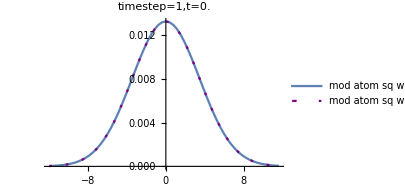
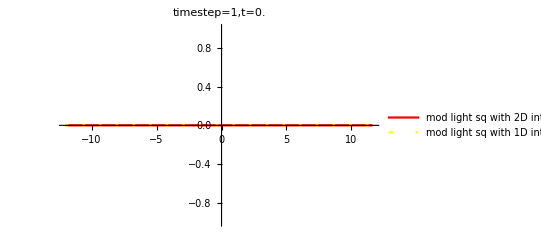
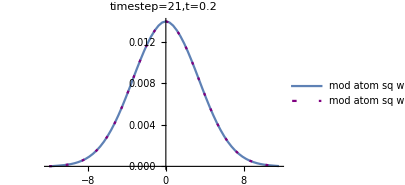
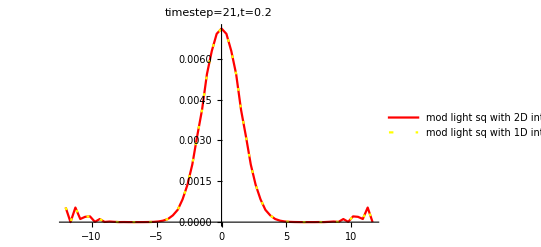
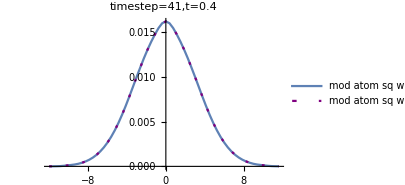
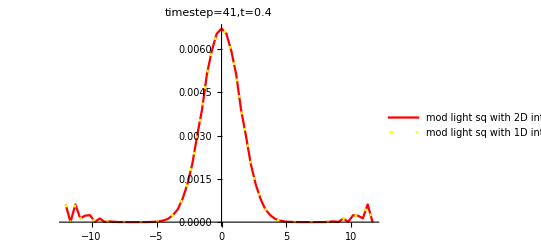
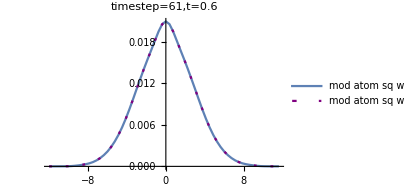
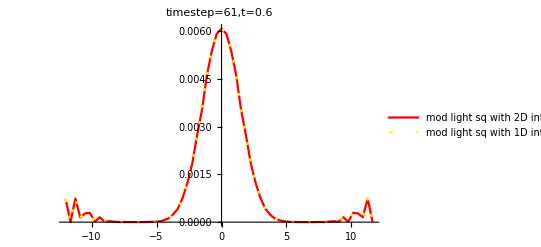

```mathematica
(* Abs val of atomic and light field by time step *)
Table[{ListLinePlot[{Table[{ x1[[i]] ,modatomsq1[[t,i,33]]} ,{i,1,xmax}],Table[{ x2[[i]] ,modatomsq2[[t,i,33]]} ,{i,1,xmax}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"mod atom sq with 2D int code","mod atom sq with 1D int code"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],modlightsq1[[t,i,33]]} ,{i,1,xmax}],Table[{ x2[[i]],modlightsq2[[t,i,33]]} ,{i,1,xmax}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Red,Thick},{Yellow,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"mod light sq with 2D int code","mod light sq with 1D int code"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Real part of atomic and light field by time step *)
```

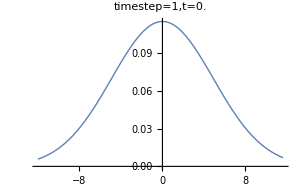
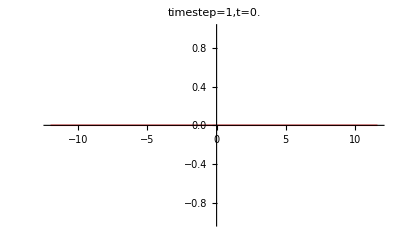
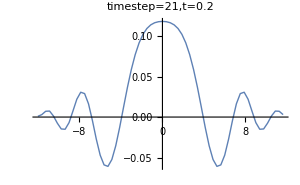
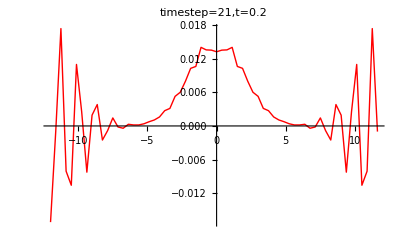
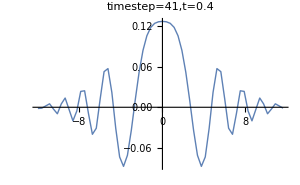
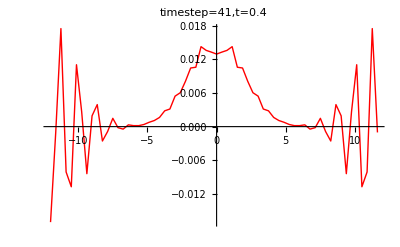
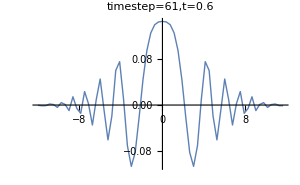
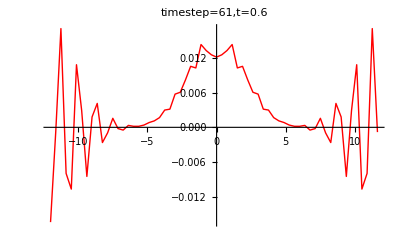

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,reatom1[[t,i,33]]} ,{i,1,xmax}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Automatic,PlotStyle->Thick,PlotRange->All],ListLinePlot[Table[{ x1[[i]],relight1[[t,i,33]]} ,{i,1,xmax}],ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{Red,Thick},PlotLegends->Automatic,PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Im part of atomic and light field by time step *)
```

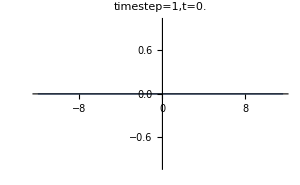
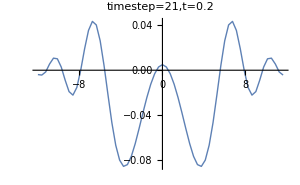
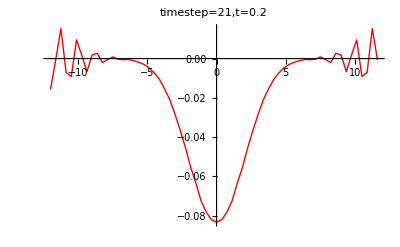
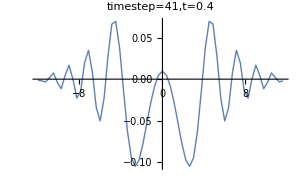
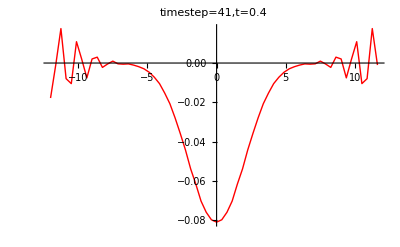
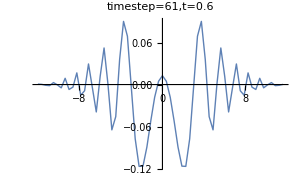
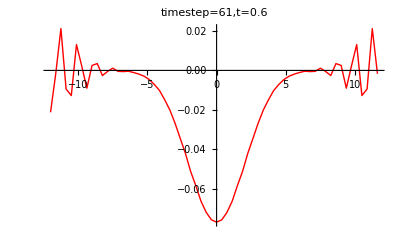
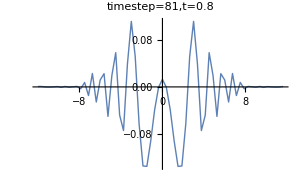
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,imatom1[[t,i,33]]} ,{i,1,xmax}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Automatic,PlotStyle->Thick,PlotRange->All],ListLinePlot[Table[{ x1[[i]],imlight1[[t,i,33]]} ,{i,1,xmax}],ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{Red,Thick},PlotLegends->Automatic,PlotRange->All]},{t,1,plotmax,plotint}]
```